# One Dimensional Random Walks with Absorption

## Milan Cvitkovic

## Introduction

A random walk with absorption is one in which the walk ends when the walker' s position reaches a certain point, the analogy being that there are 1 or more barriers located in the random walk space which will absorb the random walker if he reaches it/them.  In this notebook, we will be exploring the case in which a random walker, with equal probability of going left or right at a given step, starts at the origin and walks along a number line containing two absorption barriers, one some distance a to the left of the origin (a < 0) and one some distance b to the right of the origin (b > 0).  In this notebook we will attempt to develop code to model such a random walk with absorption with a demonstration at the end.

## Basic Code Setup:

Creating a function to generate random steps with an equal probability of L or R motion (i.e. an equal probability of outputting -1 or 1) and testing it:

```mathematica
Clear[nextStep]
nextStep := -1+2*RandomInteger[{0,1}]
nextStep
nextStep
nextStep
```

-1

1

1

## An Absorption Walk Module:

Creating a module which takes the negative and positive absorption barriers as arguments and outputs a random walk in the form of a list containing elements {steps, position on number line} until the random walker reaches a barrier:

```mathematica
Clear[AbsorptionWalk]
AbsorptionWalk[negBound_, posBound_] :=
Module[
{t,x,txList},

x = 0; t = 0; txList = {{0,0}};
While[(negBound<x<posBound),
(
x+= nextStep;
t++;
txList = Append[txList,{t,x}]
)];
txList
]
```

Plotting the above series of random walks with absorption barriers a = -2 and b = 8 using the above module (each plot is one walk, not not all axes are the same):

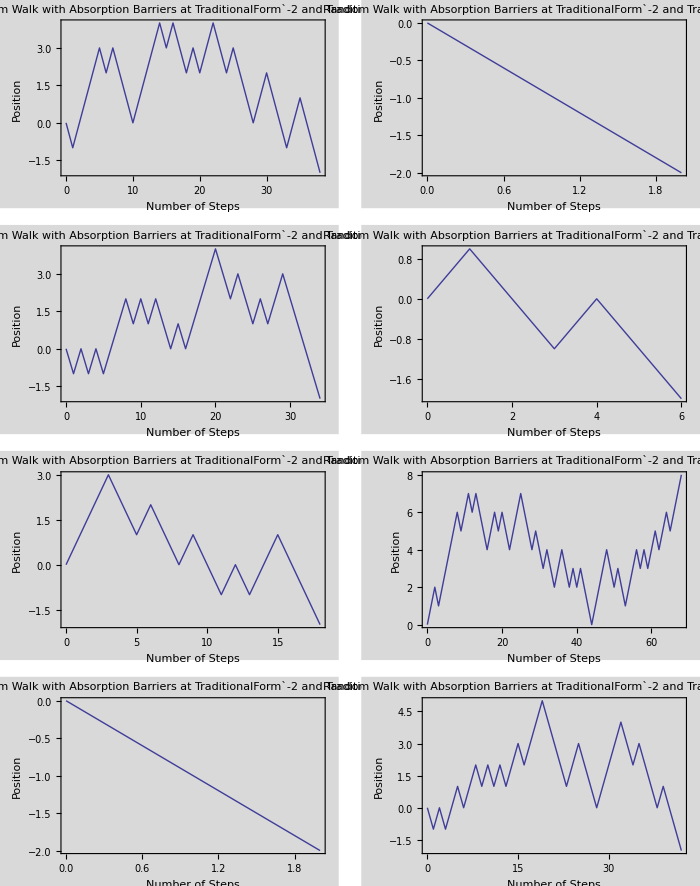

```mathematica
Clear[a,b];
a = -2;
b = 8;
PlotList= Table[ListPlot[AbsorptionWalk[a,b], Joined -> True, Frame -> True, Background -> LightGray,PlotRange->Full,FrameLabel -> {"Number of Steps","Position",""},PlotLabel -> StringForm["Random Walk with Absorption Barriers at `` and ``",a,b]],{8}];
GraphicsGrid[Partition[PlotList,2], Frame->True,ImageSize->700]
```